## Differential Operators in Cylindrical Coordinates

In tables last index corresponds to inner loop: Table[Table[a[[i, j]], {j,}], {i,}]

Actual V is covariant (indices are superscripts)

Physical coordinates require scaling with √g⟦i,i⟧

Attention with signs of Christoffels when calculating double gradients

```mathematica
Remove["Global`*"];
Off[General::spell1];
```

### Assumptions, coordinates and parametrization:

```mathematica
Ass={r>0,0<θ<π,0≤φ<2*π,{θ,φ,r,z}∈Reals};
$Assumptions=Ass;
xx={r,θ,z}; n=3; Subscript[n, 0]=1;
P={r*Cos[θ],r*Sin[θ],z};
```

### Coordinate basis (Jacobian), inverse Jacobian, metric, inverse metric, Christoffel symbols und volume measure:

```mathematica
e=Table[Table[Simplify[D[P[[ν]], xx[[μ]]],Ass],{μ,Subscript[n, 0],n}],{ν,Subscript[n, 0],n}];
J=e;
Ji=Simplify[Inverse[J],Ass];
g=Simplify[Transpose[J].J,Ass];
gi=Simplify[Inverse[g],Ass];
sdetg=Simplify[√Abs[Det[g]],Ass];
Γ=Table[Table[Table[Simplify[1/2*∑_(σ=Subscript[n, 0])^n gi[[λ,σ]]*(D[g[[σ,ν]], xx⟦μ⟧]+D[g[[μ,σ]], xx⟦ν⟧]-D[g⟦μ,ν⟧, xx⟦σ⟧]),Ass],{ν,Subscript[n, 0],n}],{μ,Subscript[n, 0],n}],{λ,Subscript[n, 0],n}];
g
```

{{1,0,0},{0,r^2,0},{0,0,1}}

```mathematica
gi
```

{{1,0,0},{0,1/r^2,0},{0,0,1}}

```mathematica
Γ
```

{{{0,0,0},{0,-r,0},{0,0,0}},{{0,1/r,0},{1/r,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
Table[Γ⟦i,2,l⟧,{i,1,3},{l,1,3}]
```

{{0,-r,0},{1/r,0,0},{0,0,0}}

### Gradient and Laplacian of a scalar function:

```mathematica
(*V=A[x1]*)
```

```mathematica
(*GradV[V_]=Table[Simplify[∂_x[[i]] V,Ass],{i,Subscript[n, 0],n}];*)
```

```mathematica
Grad0[S_]:=(temp=Table[Simplify[D[S, xx[[i]]],Ass],{i,Subscript[n, 0],n}];Expand[Simplify[Table[√gi⟦i,i⟧temp⟦i⟧,{i,1,3}],Ass]])
```

```mathematica
Grad0[S[r,θ,z]]
```

{S^(1,0,0)[r,θ,z],(S^(0,1,0)[r,θ,z])/r,S^(0,0,1)[r,θ,z]}

```mathematica
Laplace0[S_]:=(temp1=Table[Simplify[D[S, xx[[i]]],Ass],{i,Subscript[n, 0],n}];temp2=Table[Table[Simplify[D[temp1[[i]], xx[[k]]]-∑_(σ=Subscript[n, 0])^n Γ[[σ,i,k]]*temp1[[σ]],Ass],{k,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Sum[gi⟦k,k⟧temp2⟦k,k⟧,{k,1,3}]]])
```

### Gradient, Divergence and Laplacian of a vector field :

```mathematica
(*V=Simplify[Table[(√g⟦i,i⟧)^-1 Subscript[A, i][x1],{i,1,3}]]*)
```

```mathematica
(*GradV=Table[Table[Simplify[∂_x[[k]] V[[i]]+∑_(σ=Subscript[n, 0])^n Γ[[i,σ,k]]*V[[σ]],Ass],{k,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];*)
```

```mathematica
(*Expand[Simplify[Table[Table[√g⟦i,i⟧√gi⟦k,k⟧GradV⟦i,k⟧,{k,1,3}],{i,1,3}],Ass]]*)
```

```mathematica
Grad1[V_]:=(temp=Simplify[Table[(√g⟦i,i⟧)^-1 V⟦i⟧,{i,1,3}]];temp1=Table[Table[Simplify[D[temp[[i]], xx[[k]]]+∑_(σ=Subscript[n, 0])^n Γ[[i,σ,k]]*temp[[σ]],Ass],{k,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Table[Table[√g⟦i,i⟧√gi⟦k,k⟧temp1⟦i,k⟧,{k,1,3}],{i,1,3}],Ass]])
```

```mathematica
Div1[V_]:=(temp=Simplify[Table[(√g⟦i,i⟧)^-1 V⟦i⟧,{i,1,3}]];temp1=Table[Table[Simplify[D[temp[[i]], xx[[k]]]+∑_(σ=Subscript[n, 0])^n Γ[[i,σ,k]]*temp[[σ]],Ass],{k,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Sum[temp1⟦k,k⟧,{k,1,3}]]])
```

```mathematica
Laplace1[V_]:=(temp=Simplify[Table[(√g⟦i,i⟧)^-1 V⟦i⟧,{i,1,3}]];temp1=Table[Table[Simplify[D[temp[[i]], xx[[k]]]+∑_(σ=Subscript[n, 0])^n Γ[[i,σ,k]]*temp[[σ]],Ass],{k,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];temp2=Table[Table[Table[Simplify[D[temp1[[i,j]], xx[[k]]]+∑_(σ=Subscript[n, 0])^n Γ[[i,σ,k]]*temp1[[σ,j]]-∑_(σ=Subscript[n, 0])^n Γ[[σ,j,k]]*temp1[[i,σ]],Ass],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Table[√g⟦i,i⟧Sum[gi⟦k,k⟧temp2⟦i,k,k⟧,{k,1,3}],{i,1,3}]]])
```

### Divergence and Laplace of rank 2 tensor :

```mathematica
(*V=Simplify[Table[Table[(√(g⟦i,i⟧g⟦j,j⟧))^-1 Subscript[A, i,j][x],{j,1,3}],{i,1,3}]];*)
```

```mathematica
(*GradV=Table[Table[Table[Simplify[∂_x[[k]] V[[i,j]]+∑_(σ=Subscript[n, 0])^n Γ[[i,σ,k]]*V[[σ,j]]+∑_(σ=Subscript[n, 0])^n Γ[[j,σ,k]]*V[[i,σ]],Ass],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];*)
```

```mathematica
(*Expand[Simplify[Table[Table[Table[√(g⟦i,i⟧g⟦j,j⟧gi⟦k,k⟧)GradV⟦i,j,k⟧,{k,1,3}],{j,1,3}],{i,1,3}]]]*)
```

```mathematica
(*DivV=Expand[Simplify[Table[√g⟦i,i⟧Sum[GradV⟦i,k,k⟧,{k,1,3}],{i,1,3}]]]*)
```

```mathematica
(*GradGradV=Table[Table[Table[Table[Simplify[∂_x⟦l⟧ GradV⟦i,j,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,l⟧GradV⟦σ,j,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,l⟧GradV⟦i,σ,k⟧-∑_(σ=Subscript[n, 0])^n Γ⟦σ,k,l⟧GradV⟦i,j,σ⟧,Ass],{l,Subscript[n, 0],n}],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];*)
```

```mathematica
(*LaplaceV=Expand[Simplify[Table[Table[√(g⟦i,i⟧g⟦j,j⟧)Sum[gi⟦k,k⟧GradGradV⟦i,j,k,k⟧,{k,1,3}],{i,1,3}],{j,1,3}]]]*)
```

```mathematica
Div2[V_]:=(temp=Simplify[Table[Table[(√(g⟦i,i⟧g⟦j,j⟧))^-1 V⟦i,j⟧,{j,1,3}],{i,1,3}]];temp1=Table[Table[Table[Simplify[D[temp⟦i,j⟧, xx⟦k⟧]+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,k⟧temp⟦σ,j⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,k⟧temp⟦i,σ⟧,Ass],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Table[√g⟦i,i⟧Sum[temp1⟦i,k,k⟧,{k,1,3}],{i,1,3}]]])
```

```mathematica
S=Table[s[i,j][r,z],{i,1,3},{j,1,3}]
```

{{s[1,1][r,z],s[1,2][r,z],s[1,3][r,z]},{s[2,1][r,z],s[2,2][r,z],s[2,3][r,z]},{s[3,1][r,z],s[3,2][r,z],s[3,3][r,z]}}

```mathematica
Div2[S]
```

{(s[1,1][r,z])/r-(s[2,2][r,z])/r+s[1,3]^(0,1)[r,z]+s[1,1]^(1,0)[r,z],(s[1,2][r,z])/r+(s[2,1][r,z])/r+s[2,3]^(0,1)[r,z]+s[2,1]^(1,0)[r,z],(s[3,1][r,z])/r+s[3,3]^(0,1)[r,z]+s[3,1]^(1,0)[r,z]}

```mathematica
Grad2[V_]:=(temp=Simplify[Table[Table[(√(g⟦i,i⟧g⟦j,j⟧))^-1 V⟦i,j⟧,{j,1,3}],{i,1,3}]];temp1=Table[Table[Table[Simplify[D[temp⟦i,j⟧, xx⟦k⟧]+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,k⟧temp⟦σ,j⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,k⟧temp⟦i,σ⟧,Ass],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Table[Table[Table[√g⟦i,i⟧√g⟦j,j⟧√gi⟦k,k⟧temp1⟦i,j,k⟧,{k,1,3}],{j,1,3}],{i,1,3}]]])
```

```mathematica
Laplace2[V_]:=(temp=Simplify[Table[Table[(√(g⟦i,i⟧g⟦j,j⟧))^-1 V⟦i,j⟧,{j,1,3}],{i,1,3}]];temp1=Table[Table[Table[Simplify[D[temp⟦i,j⟧, xx⟦k⟧]+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,k⟧temp⟦σ,j⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,k⟧temp⟦i,σ⟧,Ass],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];temp2=Table[Table[Table[Table[Simplify[D[temp1⟦i,j,k⟧, xx⟦l⟧]+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,l⟧temp1⟦σ,j,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,l⟧temp1⟦i,σ,k⟧-∑_(σ=Subscript[n, 0])^n Γ⟦σ,k,l⟧temp1⟦i,j,σ⟧,Ass],{l,Subscript[n, 0],n}],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Table[Table[√g⟦i,i⟧ √g⟦j,j⟧Sum[gi⟦k,k⟧temp2⟦i,j,k,k⟧,{k,1,3}],{i,1,3}],{j,1,3}]]])
```

### Divergence and Laplace of rank 3 tensor :

```mathematica
Div3[V_]:=(temp=Simplify[Table[Table[Table[(√(g⟦i,i⟧g⟦j,j⟧g⟦k,k⟧))^-1 V⟦i,j,k⟧,{k,1,3}],{j,1,3}],{i,1,3}]];temp1=Table[Table[Table[Table[Simplify[D[temp⟦i,j,k⟧, xx⟦l⟧]+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,l⟧temp⟦σ,j,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,l⟧temp⟦i,σ,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦k,σ,l⟧temp⟦i,j,σ⟧,Ass],{l,Subscript[n, 0],n}],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Table[Table[√(g⟦i,i⟧g⟦j,j⟧)Sum[temp1⟦i,j,k,k⟧,{k,1,3}],{j,1,3}],{i,1,3}]]])
```

```mathematica
S=Table[s[i,j,k][r],{i,1,3},{j,1,3},{k,1,3}]
```

{{{s[1,1,1][r],s[1,1,2][r],s[1,1,3][r]},{s[1,2,1][r],s[1,2,2][r],s[1,2,3][r]},{s[1,3,1][r],s[1,3,2][r],s[1,3,3][r]}},{{s[2,1,1][r],s[2,1,2][r],s[2,1,3][r]},{s[2,2,1][r],s[2,2,2][r],s[2,2,3][r]},{s[2,3,1][r],s[2,3,2][r],s[2,3,3][r]}},{{s[3,1,1][r],s[3,1,2][r],s[3,1,3][r]},{s[3,2,1][r],s[3,2,2][r],s[3,2,3][r]},{s[3,3,1][r],s[3,3,2][r],s[3,3,3][r]}}}

```mathematica
Div3[S]
```

{{(s[1,1,1][r])/r-(s[1,2,2][r])/r-(s[2,1,2][r])/r+s[1,1,1]'[r],(s[1,1,2][r])/r+(s[1,2,1][r])/r-(s[2,2,2][r])/r+s[1,2,1]'[r],(s[1,3,1][r])/r-(s[2,3,2][r])/r+s[1,3,1]'[r]},{(s[1,1,2][r])/r+(s[2,1,1][r])/r-(s[2,2,2][r])/r+s[2,1,1]'[r],(s[1,2,2][r])/r+(s[2,1,2][r])/r+(s[2,2,1][r])/r+s[2,2,1]'[r],(s[1,3,2][r])/r+(s[2,3,1][r])/r+s[2,3,1]'[r]},{(s[3,1,1][r])/r-(s[3,2,2][r])/r+s[3,1,1]'[r],(s[3,1,2][r])/r+(s[3,2,1][r])/r+s[3,2,1]'[r],(s[3,3,1][r])/r+s[3,3,1]'[r]}}

```mathematica
(s[1,1,1][r])/r-2(s[1,2,2][r])/r+s[1,1,1]'[r]
```

(s[1,1,1][r])/r-(2 s[1,2,2][r])/r+s[1,1,1]'[r]

```mathematica
Grad3[V_]:=(temp=Simplify[Table[Table[Table[(√(g⟦i,i⟧g⟦j,j⟧g⟦k,k⟧))^-1 V⟦i,j,k⟧,{k,1,3}],{j,1,3}],{i,1,3}]];temp1=Table[Table[Table[Table[Simplify[D[temp⟦i,j,k⟧, x⟦l⟧]+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,l⟧temp⟦σ,j,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,l⟧temp⟦i,σ,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦k,σ,l⟧temp⟦i,j,σ⟧,Ass],{l,Subscript[n, 0],n}],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];

Expand[Simplify[Table[Table[Table[Table[√g⟦i,i⟧√g⟦j,j⟧√g⟦k,k⟧√gi⟦l,l⟧temp1⟦i,j,k,l⟧,{l,1,3}],{k,1,3}],{j,1,3}],{i,1,3}]]])
```

```mathematica
Laplace3[V_]:=(temp=Simplify[Table[Table[Table[(√(g⟦i,i⟧g⟦j,j⟧g⟦k,k⟧))^-1 V⟦i,j,k⟧,{k,1,3}],{j,1,3}],{i,1,3}]];temp1=Table[Table[Table[Table[Simplify[D[temp⟦i,j,k⟧, x⟦l⟧]+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,l⟧temp⟦σ,j,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,l⟧temp⟦i,σ,k⟧+∑_(σ=Subscript[n, 0])^n Γ⟦k,σ,l⟧temp⟦i,j,σ⟧,Ass],{l,Subscript[n, 0],n}],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];temp2=Table[Table[Table[Table[Table[Simplify[D[temp1⟦i,j,k,l⟧, x⟦m⟧]+∑_(σ=Subscript[n, 0])^n Γ⟦i,σ,m⟧temp1⟦σ,j,k,l⟧+∑_(σ=Subscript[n, 0])^n Γ⟦j,σ,m⟧temp1⟦i,σ,k,l⟧+∑_(σ=Subscript[n, 0])^n Γ⟦k,σ,m⟧temp1⟦i,j,σ,l⟧-∑_(σ=Subscript[n, 0])^n Γ⟦σ,l,m⟧temp1⟦i,j,k,σ⟧,Ass],{m,Subscript[n, 0],n}],{l,Subscript[n, 0],n}],{k,Subscript[n, 0],n}],{j,Subscript[n, 0],n}],{i,Subscript[n, 0],n}];Expand[Simplify[Table[Table[Table[√g⟦i,i⟧ √g⟦j,j⟧√g⟦k,k⟧Sum[gi⟦l,l⟧temp2⟦i,j,k,l,l⟧,{l,1,3}],{k,1,3}],{j,1,3}],{i,1,3}]]])
```

0-1-2-3 system (Type B)

## first order 0-1-2-3-system with 1-2-3-relaxation

### Final Result

```mathematica
coef[expr_,var_]:=Flatten[Normal[CoefficientArrays[expr,var]]];Clear[A0,A1,A2,τ,λ1,λ2,λ3,a0,b0,d0,κ0,γ0,ω0,a,b,d,γ,κ,ω,C0,C1,C2,C3,C4,C5,C6,C7,C8,C9,C11,C12,K1,K2,K3,K4,K5,K6,K7,K8,K9,K10,K11,K12]

p[r_,θ_]=d0[r]+d[r]Cos[θ];

ur[r_,θ_]=a0[r]+a[r]Cos[θ];
uθ[r_,θ_]=b0[r]-b[r]Sin[θ];
u[r_,θ_]={ur[r,θ],uθ[r,θ],0};

σrr[r_,θ_]=γ0[r]+γ[r]Cos[θ];
σθθ[r_,θ_]=ω0[r]-ω[r]Cos[θ];
σrθ[r_,θ_]=κ0[r]+κ[r]Sin[θ];
σ[r_,θ_]={{σrr[r,θ],σrθ[r,θ],0},{σrθ[r,θ],σθθ[r,θ],0},{0,0,-σrr[r,θ]-σθθ[r,θ]}};

{mrrr[r_,θ_],mrrθ[r_,θ_],mrθθ[r_,θ_],mθθθ[r_,θ_]}= τ{(2 γ0[r])/(5 r)-(2 ω0[r])/(5 r)-(3 γ0'[r])/5+((2 γ[r])/(5 r)+(2 κ[r])/(5 r)+(2 ω[r])/(5 r)-(3 γ'[r])/5)Cos[θ],(14 κ0[r])/(15 r)-(8 κ0'[r])/15+(γ[r]/(3 r)+(14 κ[r])/(15 r)+(2 ω[r])/(15 r)-(8 κ'[r])/15)Sin[θ],-(8 γ0[r])/(15 r)+(8 ω0[r])/(15 r)+(2 γ0'[r])/15-ω0'[r]/3+(-(8 γ[r])/(15 r)-(8 κ[r])/(15 r)-(8 ω[r])/(15 r)+(2 γ'[r])/15+ω'[r]/3)Cos[θ],-(6 κ0[r])/(5 r)+(2 κ0'[r])/5+(-(6 κ[r])/(5 r)-(3 ω[r])/(5 r)+(2 κ'[r])/5)Sin[θ]};

F[r_,θ_]=A0+A2 r^2+A1(1-(5 r^2)/(18 τ^2))Cos[θ];
```

```mathematica
λ3=√(3/2);
λ2=√(5/6);
λ1=√(15/31);
BI[i_,x_]=BesselI[i,x];
BK[i_,x_]=BesselK[i,x];

withτ={r->r/τ};

d0[r_]=τ(-(6 A0)/5+(32 τ^2 A2)/5-(A0/4-(4 τ^2 A2)/3) r^2-(τ^2 A2)/16 r^4)+C0+C3 Log[r]+K3 BK[0,λ2 r]+K4 (BI[0,λ2 r]-1)/.withτ;
d[r_]=τ(-(19 A1 r^2)/27+(A1 r^4)/54)+C1/r+C2 r+K1 BI[1,λ2 r]+K2 BK[1,λ2 r]/.withτ;

a0[r_]=τ((A0 r)/2+(τ^2 A2 r^3)/4)-C3/r/.withτ;
a[r_]=τ((2 A1 r)/3-(2 A1 r^3)/27)-C2+C1/r^2+K7 BI[1,λ1 r]/r+K8 BK[1,λ1 r]/r/.withτ;
b0[r_]=K5 BI[1,λ1 r]+K6 BK[1,λ1 r]/.withτ;
b[r_]=τ((A1 r)/3-(A1 r^3)/54)-C2-C1/r^2+K7(r λ1 BI[0,r λ1]-BI[1,r λ1])/r-K8(r λ1 BK[0,r λ1]+BK[1,r λ1])/r/.withτ;

κ0[r_]=-K5 BI[2,λ1 r]/λ1+K6 BK[2,λ1 r]/λ1/.withτ;
κ[r_]=τ(-(A1 r^2)/9)+(4 C1)/r^3+(3 K1 BI[2,r λ2])/(2 r λ2)+(2 K11 BI[2,r λ3])/(r λ3)+K7 ((2 BI[2,r λ1])/(r λ1)+BI[3,r λ1])-(3 K2 BK[2,r λ2])/(2 r λ2)-(2 K12 BK[2,r λ3])/(r λ3)+K8 (-(2 BK[2,r λ1])/(r λ1)+BK[3,r λ1])/.withτ;
γ0[r_]=τ(-A0/3-(8 τ^2 A2)/5-(5 τ^2 A2)/6 r^2)-(2 C3)/r^2+(K9 BI[1,r λ3])/(r λ3)+K4 (-BI[1,r λ2]/(2 r λ2)-BI[2,r λ2])+(K10 BK[1,r λ3])/(r λ3)+K3 (BK[1,r λ2]/(2 r λ2)-BK[2,r λ2])/.withτ;
γ[r_]=τ((7 A1 r^2)/27)+(4 C1)/r^3-(2 K7 BI[2,r λ1])/(r λ1)+K1 (-BI[1,r λ2]+(3 BI[2,r λ2])/(2 r λ2))+(2 K11 BI[2,r λ3])/(r λ3)+(2 K8 BK[2,r λ1])/(r λ1)+K2 (-BK[1,r λ2]-(3 BK[2,r λ2])/(2 r λ2))-(2 K12 BK[2,r λ3])/(r λ3)/.withτ;
ω0[r_]=τ((τ^2 A2 r^2)/6-A0/3-(8 τ^2 A2)/5)+(2 C3)/r^2+K4 (1/2 BI[0,r λ2]-(3 BI[1,r λ2])/(2 r λ2))+K9 (BI[0,r λ3]-BI[1,r λ3]/(r λ3))+K3 (1/2 BK[0,r λ2]+(3 BK[1,r λ2])/(2 r λ2))+K10 (-BK[0,r λ3]-BK[1,r λ3]/(r λ3))/.withτ;
ω[r_]=τ((2 A1 r^2)/27)+(4 C1)/r^3-(2 K7 BI[2,r λ1])/(r λ1)+K1 (-1/2 BI[1,r λ2]+(3 BI[2,r λ2])/(2 r λ2))+K11 (-2 BI[1,r λ3]+(2 BI[2,r λ3])/(r λ3))+(2 K8 BK[2,r λ1])/(r λ1)+K2 (-1/2 BK[1,r λ2]-(3 BK[2,r λ2])/(2 r λ2))+K12 (-2 BK[1,r λ3]-(2 BK[2,r λ3])/(r λ3))/.withτ;
```

```mathematica
TraceFreeSym2[mat_]:=1/2(mat+Transpose[mat])-1/3 Tr[mat]IdentityMatrix[3];
TraceFreeSym3[mat_]:=Block[{perm,sym1,trace},
perm=Permutations[{1,2,3}];
sym1=Expand[1/Length[perm] Sum[Transpose[mat,idx],{idx,perm}]];
trace=Sum[sym1⟦All,jj,jj⟧,{jj,1,3}];
Expand[sym1-1/5 Table[trace⟦ii⟧KroneckerDelta[jj,kk]+trace⟦jj⟧KroneckerDelta[ii,kk]+trace⟦kk⟧KroneckerDelta[ii,jj],{ii,1,3},{jj,1,3},{kk,1,3}]]
]
```

```mathematica
Simplify[
{coef[Div1[u[r,θ]]-F[r,θ],{Cos[θ],Sin[θ]}],
coef[Grad0[p[r,θ]]+Div2[σ[r,θ]]+1/τ u[r,θ],{Cos[θ],Sin[θ]}],
coef[2TraceFreeSym2[Grad1[u[r,θ]]]+1/τ σ[r,θ]-2τ Div3[TraceFreeSym3[Grad2[σ[r,θ]]]],{Cos[θ],Sin[θ]}],
coef[1/τ{mrrr[r,θ],mrrθ[r,θ],mrθθ[r,θ],mθθθ[r,θ]}+Extract[TraceFreeSym3[Grad2[σ[r,θ]]],{{1,1,1},{1,1,2},{1,2,2},{2,2,2}}],{Cos[θ],Sin[θ]}]
}]
```

```mathematica
{{0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}
```

```mathematica
{{0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}
```

```mathematica
Clear[λ1,λ2,λ3]
```

```mathematica
coef[Expand[ur[R,θ]-p[R,θ]],{Cos[θ],Sin[θ]}]
coef[Expand[mrrr[R,θ]-σrr[R,θ]],{Cos[θ],Sin[θ]}]
coef[Expand[σrθ[R,θ]-uθ[R,θ]],{Cos[θ],Sin[θ]}]
coef[Expand[mrθθ[R,θ]-σθθ[R,θ]],{Cos[θ],Sin[θ]}]
```

{-C0-C3/R-K4 BesselI[0,R λ2]-K3 BesselK[0,R λ2]-C3 Log[R],-C2+C1/R^2-C1/R-C2 R+(K7 BesselI[1,R λ1])/R-K1 BesselI[1,R λ2]+(K8 BesselK[1,R λ1])/R-K2 BesselK[1,R λ2],0}

{-(4 C3)/R^3+(2 C3)/R^2-(K4 BesselI[0,R λ2])/(20 R)-(7 K9 BesselI[0,R λ3])/(10 R)+(K4 BesselI[1,R λ2])/(10 R^2 λ2)+(K4 BesselI[1,R λ2])/(2 R λ2)+3/10 K4 λ2 BesselI[1,R λ2]+(7 K9 BesselI[1,R λ3])/(5 R^2 λ3)-(K9 BesselI[1,R λ3])/(R λ3)+K4 BesselI[2,R λ2]-(K4 BesselI[2,R λ2])/(4 R)-(3 K9 BesselI[2,R λ3])/(10 R)+3/10 K4 λ2 BesselI[3,R λ2]-(K3 BesselK[0,R λ2])/(20 R)+(7 K10 BesselK[0,R λ3])/(10 R)-(K3 BesselK[1,R λ2])/(10 R^2 λ2)-(K3 BesselK[1,R λ2])/(2 R λ2)-3/10 K3 λ2 BesselK[1,R λ2]+(7 K10 BesselK[1,R λ3])/(5 R^2 λ3)-(K10 BesselK[1,R λ3])/(R λ3)+K3 BesselK[2,R λ2]-(K3 BesselK[2,R λ2])/(4 R)+(3 K10 BesselK[2,R λ3])/(10 R)-3/10 K3 λ2 BesselK[3,R λ2],(12 C1)/R^4-(4 C1)/R^3+3/10 K1 λ2 BesselI[0,R λ2]+(3 K7 BesselI[1,R λ1])/(5 R)+K1 BesselI[1,R λ2]-(21 K1 BesselI[1,R λ2])/(20 R)-(7 K11 BesselI[1,R λ3])/(5 R)-(2 K7 BesselI[2,R λ1])/(R^2 λ1)+(2 K7 BesselI[2,R λ1])/(R λ1)+(27 K1 BesselI[2,R λ2])/(10 R^2 λ2)-(3 K1 BesselI[2,R λ2])/(2 R λ2)+3/10 K1 λ2 BesselI[2,R λ2]+(18 K11 BesselI[2,R λ3])/(5 R^2 λ3)-(2 K11 BesselI[2,R λ3])/(R λ3)+(K7 BesselI[3,R λ1])/R-(9 K1 BesselI[3,R λ2])/(20 R)-(3 K11 BesselI[3,R λ3])/(5 R)-3/10 K2 λ2 BesselK[0,R λ2]+(3 K8 BesselK[1,R λ1])/(5 R)+K2 BesselK[1,R λ2]-(21 K2 BesselK[1,R λ2])/(20 R)-(7 K12 BesselK[1,R λ3])/(5 R)+(2 K8 BesselK[2,R λ1])/(R^2 λ1)-(2 K8 BesselK[2,R λ1])/(R λ1)-(27 K2 BesselK[2,R λ2])/(10 R^2 λ2)+(3 K2 BesselK[2,R λ2])/(2 R λ2)-3/10 K2 λ2 BesselK[2,R λ2]-(18 K12 BesselK[2,R λ3])/(5 R^2 λ3)+(2 K12 BesselK[2,R λ3])/(R λ3)+(K8 BesselK[3,R λ1])/R-(9 K2 BesselK[3,R λ2])/(20 R)-(3 K12 BesselK[3,R λ3])/(5 R),0}

{-K5 BesselI[1,R λ1]-(K5 BesselI[2,R λ1])/λ1-K6 BesselK[1,R λ1]+(K6 BesselK[2,R λ1])/λ1,0,-C2+(4 C1)/R^3-C1/R^2+K7 λ1 BesselI[0,R λ1]-(K7 BesselI[1,R λ1])/R+(2 K7 BesselI[2,R λ1])/(R λ1)+(3 K1 BesselI[2,R λ2])/(2 R λ2)+(2 K11 BesselI[2,R λ3])/(R λ3)+K7 BesselI[3,R λ1]-K8 λ1 BesselK[0,R λ1]-(K8 BesselK[1,R λ1])/R-(2 K8 BesselK[2,R λ1])/(R λ1)-(3 K2 BesselK[2,R λ2])/(2 R λ2)-(2 K12 BesselK[2,R λ3])/(R λ3)+K8 BesselK[3,R λ1]}

{(4 C3)/R^3-(2 C3)/R^2-1/2 K4 BesselI[0,R λ2]+(29 K4 BesselI[0,R λ2])/(60 R)-K9 BesselI[0,R λ3]+(23 K9 BesselI[0,R λ3])/(30 R)-(29 K4 BesselI[1,R λ2])/(30 R^2 λ2)+(3 K4 BesselI[1,R λ2])/(2 R λ2)-7/30 K4 λ2 BesselI[1,R λ2]-(23 K9 BesselI[1,R λ3])/(15 R^2 λ3)+(K9 BesselI[1,R λ3])/(R λ3)-1/3 K9 λ3 BesselI[1,R λ3]+(3 K4 BesselI[2,R λ2])/(4 R)+(7 K9 BesselI[2,R λ3])/(30 R)-1/15 K4 λ2 BesselI[3,R λ2]-1/2 K3 BesselK[0,R λ2]+(29 K3 BesselK[0,R λ2])/(60 R)+K10 BesselK[0,R λ3]-(23 K10 BesselK[0,R λ3])/(30 R)+(29 K3 BesselK[1,R λ2])/(30 R^2 λ2)-(3 K3 BesselK[1,R λ2])/(2 R λ2)+7/30 K3 λ2 BesselK[1,R λ2]-(23 K10 BesselK[1,R λ3])/(15 R^2 λ3)+(K10 BesselK[1,R λ3])/(R λ3)-1/3 K10 λ3 BesselK[1,R λ3]+(3 K3 BesselK[2,R λ2])/(4 R)-(7 K10 BesselK[2,R λ3])/(30 R)+1/15 K3 λ2 BesselK[3,R λ2],-(12 C1)/R^4+(4 C1)/R^3-3/20 K1 λ2 BesselI[0,R λ2]-1/3 K11 λ3 BesselI[0,R λ3]-(7 K7 BesselI[1,R λ1])/(15 R)-1/2 K1 BesselI[1,R λ2]+(23 K1 BesselI[1,R λ2])/(20 R)-2 K11 BesselI[1,R λ3]+(23 K11 BesselI[1,R λ3])/(15 R)+(2 K7 BesselI[2,R λ1])/(R^2 λ1)-(2 K7 BesselI[2,R λ1])/(R λ1)-(31 K1 BesselI[2,R λ2])/(10 R^2 λ2)+(3 K1 BesselI[2,R λ2])/(2 R λ2)-3/20 K1 λ2 BesselI[2,R λ2]-(62 K11 BesselI[2,R λ3])/(15 R^2 λ3)+(2 K11 BesselI[2,R λ3])/(R λ3)-1/3 K11 λ3 BesselI[2,R λ3]-(K7 BesselI[3,R λ1])/R+(7 K1 BesselI[3,R λ2])/(20 R)+(7 K11 BesselI[3,R λ3])/(15 R)+3/20 K2 λ2 BesselK[0,R λ2]+1/3 K12 λ3 BesselK[0,R λ3]-(7 K8 BesselK[1,R λ1])/(15 R)-1/2 K2 BesselK[1,R λ2]+(23 K2 BesselK[1,R λ2])/(20 R)-2 K12 BesselK[1,R λ3]+(23 K12 BesselK[1,R λ3])/(15 R)-(2 K8 BesselK[2,R λ1])/(R^2 λ1)+(2 K8 BesselK[2,R λ1])/(R λ1)+(31 K2 BesselK[2,R λ2])/(10 R^2 λ2)-(3 K2 BesselK[2,R λ2])/(2 R λ2)+3/20 K2 λ2 BesselK[2,R λ2]+(62 K12 BesselK[2,R λ3])/(15 R^2 λ3)-(2 K12 BesselK[2,R λ3])/(R λ3)+1/3 K12 λ3 BesselK[2,R λ3]-(K8 BesselK[3,R λ1])/R+(7 K2 BesselK[3,R λ2])/(20 R)+(7 K12 BesselK[3,R λ3])/(15 R),0}

### With Boundary Conditions (large radius)

```mathematica
Clear[χ]
{BCrhs,BC}=Normal[CoefficientArrays[
{-sn+χ((θ-θW)),
-Rnt+χ(st+2mnnt-uW),
-mnnn+χ(Rnn),
-mntt+χ(Rtt)},{θ,sn,st,Rnn,Rnt,Rtt,mnnn,mnnt,mntt,mttt}]]
```

{{-θW χ,-uW χ,0,0},{{χ,-1,0,0,0,0,0,0,0,0},{0,0,χ,0,-1,0,0,2 χ,0,0},{0,0,0,χ,0,0,-1,0,0,0},{0,0,0,0,0,χ,0,0,-1,0}}}

```mathematica
vars=Table[u[i],{i,1,10}];
{BC1rhs,BC1}=Normal[CoefficientArrays[vars/.Solve[BC.vars+BCrhs==0,vars⟦{2,5,7,9}⟧]⟦1⟧,vars]];
```

```mathematica
Expand[(BC1.vars+BC1rhs)-IdentityMatrix[10].vars]
Expand[(BC.vars+BCrhs)]
```

{0,-2 θW χ+2 χ u[1]-u[2]+5/28 χ u[4],0,0,-(11 uW χ)/5+11/5 χ u[3]-u[5]+22/5 χ u[8],0,(6 θW χ)/5-6/5 χ u[1]+93/70 χ u[4]-u[7],0,-(3 θW χ)/5+3/5 χ u[1]-111/280 χ u[4]+15/28 χ u[6]-u[9],0}

{-θW χ+χ u[1]-u[2]/2+5/56 χ u[4],-uW χ+χ u[3]-(5 u[5])/11+2 χ u[8],(28 θW χ)/31-28/31 χ u[1]+χ u[4]-(70 u[7])/93,-(28 θW χ)/25+28/25 χ u[1]-37/50 χ u[4]+χ u[6]-(28 u[9])/15}

```mathematica
Map[{#⟦1⟧-{1,1},#⟦2⟧}&,Drop[ArrayRules[SparseArray[BC1]],-1]]
Map[{#⟦1⟧-{1},#⟦2⟧}&,Drop[ArrayRules[SparseArray[BC1rhs]],-1]]
```

{{{0,0},1},{{1,0},2 χ},{{1,3},(5 χ)/28},{{2,2},1},{{3,3},1},{{4,2},(11 χ)/5},{{4,7},(22 χ)/5},{{5,5},1},{{6,0},-(6 χ)/5},{{6,3},(93 χ)/70},{{7,7},1},{{8,0},(3 χ)/5},{{8,3},-(111 χ)/280},{{8,5},(15 χ)/28},{{9,9},1}}

{{{1},-2 θW χ},{{4},-(11 uW χ)/5},{{6},(6 θW χ)/5},{{8},-(3 θW χ)/5}}

```mathematica
R0=1/2;
R1=2;
τ=1.0;
χ=1;
θ0=2;
θ1=1;
uW0=0;
A0=0;
A1=0;
A2=1/10;

scaling1={C1->C1/τ,K1->BI[1,λ2 R1/τ]^-1 K1,K2->BK[1,λ2 R0/τ]^-1 K2,
K3->BK[0,λ2 R0/τ]^-1 K3,K4->BI[0,λ2 R1/τ]^-1 K4,
K7->BI[1,λ1 R1/τ]^-1 K7,K8->BK[1,λ1 R0/τ]^-1 K8,
K9->BI[1,λ3 R1/τ]^-1 K9,K10->BK[1,λ3 R0/τ]^-1 K10,
K11->BI[2,λ3 R1/τ]^-1 K11,K12->BK[2,λ3 R0/τ]^-1 K12};
scaling={};
```

```mathematica
C1=C2=K1=K2=K5=K6=K7=K8=K11=K12=0;
U[r_,θ_]:={p[r,θ],nn[r]ur[r,θ],uθ[r,θ],σrr[r,θ],nn[r]σrθ[r,θ],σθθ[r,θ],nn[r]mrrr[r,θ],mrrθ[r,θ],nn[r]mrθθ[r,θ],mθθθ[r,θ]};nn[R0]=-1;
nn[R1]=1;

solbc=Solve[(Join[
coef[Expand[BC.U[R0,θ]+BCrhs/.{θW->θ0,uW->uW0 Sin[θ]}],{Cos[θ],Sin[θ]}],
coef[Expand[BC.U[R1,θ]+BCrhs/.{θW->θ1,uW->0}],{Cos[θ],Sin[θ]}]
]/.scaling)==0,{C0,C3,K3,K4,K9,K10}]⟦1⟧
```

{C0→0.758179,C3→-0.168077,K3→0.136182,K4→-0.439713,K9→0.0330095,K10→-0.155614}

```mathematica
{bBC,ABC}=FunctionExpand[Simplify[Normal[CoefficientArrays[Select[Join[
coef[Expand[BC.U[R0,θ]+BCrhs/.{θW->θ0,uW->uW0 Sin[θ]}],{Cos[θ],Sin[θ]}],
coef[Expand[BC.U[R1,θ]+BCrhs/.{θW->θ1,uW->0}],{Cos[θ],Sin[θ]}]
]/.scaling1,Length[#]>0&],{C0,C3,K3,K4,K9,K10}]]]];
```

```mathematica
scale1=DiagonalMatrix[{1,τ^-2,τ^-2,1,τ^-2,τ^-2}];
scale2=DiagonalMatrix[{1,1,(BesselK[0,λ2/(R1 τ)])^-1,τ^2(BesselI[0,λ2/(R0 τ)])^-1,τ^2(BesselI[0,λ3/(R0 τ)])^-1,(BesselK[0,λ3/(R1 τ)])^-1}];
Thread[{C0,C3,K3,K4,K9,K10}->-scale2.Inverse[scale1.ABC.scale2/.{τ->100.0}].scale1.bBC/.{τ->100.0}]
```

{C0→-639999.,C3→-0.00297606,K3→0.00231834,K4→-640556.,K9→-277.915,K10→-0.00266869}

```mathematica
CForm[{C0,C1,C2,C3,K1,K2,K3,K4,K7,K8}/.scaling/.solbc]
```

List(1.8779973238556051,0.48170199857369206,-0.032245279747091384,0.08526741914275243,5.806990250981511e-9,5.91399305082199,
   -1.316040533386685,-1.171551028043168e-8,-2.0241640291810703e-8,1.4316433131003932)

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

pC[x_,y_]=p[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{ux[x_,y_],uy[x_,y_]}={ur[√(x^2+y^2),ArcTan[x,y]],uθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{σxx[x_,y_],σxy[x_,y_]},{σyx[x_,y_],σyy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{σrr[√(x^2+y^2),ArcTan[x,y]],σrθ[√(x^2+y^2),ArcTan[x,y]]},{σrθ[√(x^2+y^2),ArcTan[x,y]],σθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[pC[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1],PlotRange->All]
```

```mathematica
Plot3D[ux[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

## first order 0-1-2-3-System with 2-3-relaxation

### Final Result

```mathematica
coef[expr_,var_]:=Flatten[Normal[CoefficientArrays[expr,var]]];
TraceFreeSym2[mat_]:=1/2(mat+Transpose[mat])-1/3 Tr[mat]IdentityMatrix[3];
TraceFreeSym3[mat_]:=Block[{perm,sym1,trace},
perm=Permutations[{1,2,3}];
sym1=Expand[1/Length[perm] Sum[Transpose[mat,idx],{idx,perm}]];
trace=Sum[sym1⟦All,jj,jj⟧,{jj,1,3}];
Expand[sym1-1/5 Table[trace⟦ii⟧KroneckerDelta[jj,kk]+trace⟦jj⟧KroneckerDelta[ii,kk]+trace⟦kk⟧KroneckerDelta[ii,jj],{ii,1,3},{jj,1,3},{kk,1,3}]]
]
```

```mathematica
Clear[τ,λ1,λ2,λ3,a0,b0,d0,κ0,γ0,ω0,a,b,d,γ,κ,ω,C0,C1,C2,C3,C4,C5,C6,C7,C8,C9,C10,C11,C12,K1,K2,K3,K4,K5,K6,K7,K8,K9,K10,K11,K12]

ur[r_,θ_] = a0[r]+Cos[θ]a[r];
uθ[r_,θ_] = b0[r]-Sin[θ] b[r];

u[r_,θ_]={ur[r,θ],uθ[r,θ],0};

p[r_,θ_] = d0[r]+d[r]Cos[θ];


σrr[r_,θ_]=Cos[θ] γ[r]+γ0[r];
σθθ[r_,θ_]=-(Cos[θ] ω[r]+ω0[r]);
σrθ[r_,θ_]=κ0[r]+Sin[θ]κ[r];
σzz[r_,θ_]=-σrr[r,θ]-σθθ[r,θ];

σ[r_,θ_]={{σrr[r,θ],σrθ[r,θ],0},{σrθ[r,θ],σθθ[r,θ],0},{0,0,σzz[r,θ]}};

{mrrr[r_,θ_],mrrθ[r_,θ_],mrθθ[r_,θ_],mθθθ[r_,θ_]}=τ {(2 γ0[r])/(5 r)+(2 ω0[r])/(5 r)+Cos[θ] ((2 γ[r])/(5 r)+(2 κ[r])/(5 r)+(2 ω[r])/(5 r)-(3 γ'[r])/5)-(3 γ0'[r])/5,(14 κ0[r])/(15 r)+Sin[θ] (γ[r]/(3 r)+(14 κ[r])/(15 r)+(2 ω[r])/(15 r)-(8 κ'[r])/15)-(8 κ0'[r])/15,-(8 γ0[r])/(15 r)-(8 ω0[r])/(15 r)+(2 γ0'[r])/15+Cos[θ] (-(8 γ[r])/(15 r)-(8 κ[r])/(15 r)-(8 ω[r])/(15 r)+(2 γ'[r])/15+ω'[r]/3)+ω0'[r]/3,-(6 κ0[r])/(5 r)+Sin[θ] (-(6 κ[r])/(5 r)-(3 ω[r])/(5 r)+(2 κ'[r])/5)+(2 κ0'[r])/5};
mrzz[r_,θ_]=-mrrr[r,θ]-mrθθ[r,θ];
```

```mathematica
eqns={coef[Div1[u[r,θ]],{Cos[θ],Sin[θ]}],
coef[Grad0[p[r,θ]]+Div2[σ[r,θ]],{Cos[θ],Sin[θ]}],
coef[2TraceFreeSym2[Grad1[u[r,θ]]]+1/τ σ[r,θ]-2τ Div3[TraceFreeSym3[Grad2[σ[r,θ]]]],{Cos[θ],Sin[θ]}],
coef[1/τ{mrrr[r,θ],mrrθ[r,θ],mrθθ[r,θ],mθθθ[r,θ]}+Extract[TraceFreeSym3[Grad2[σ[r,θ]]],{{1,1,1},{1,1,2},{1,2,2},{2,2,2}}],{Cos[θ],Sin[θ]}]
};
```

```mathematica
withτ={r->r/τ};
λ2=√(5/6);
λ3=√(3/2);
BI[i_,x_]=BesselI[i,x];
BK[i_,x_]=BesselK[i,x];

d[r_]=C1/r+C2 r+K1 BI[1,λ2 r]+K2 BK[1,λ2 r]/.withτ;
d0[r_]=C8+K3 BK[0,λ2 r]+K4 BI[0,λ2 r]/.withτ;

a0[r_]=C3/2 1/r/.withτ;
b0[r_]=C7 r+C4/(2r)/.withτ;
a[r_]=(C2 r^2)/8-C6/r^2+C5-1/2 C1 Log[r]/.withτ;
b[r_]=C5+C6/r^2+(3 C2 r^2)/8+C1 (-1/2-Log[r]/2)/.withτ;

κ0[r_]=C4/r^2/.withτ;

γ0[r_]=C3/r^2+(K8 BI[1,r λ3])/r+K4 (-BI[1,r λ2]/(2 r λ2)-BI[2,r λ2])+(K7 BK[1,r λ3])/r+K3 (BK[1,r λ2]/(2 r λ2)-BK[2,r λ2])/.withτ;

ω0[r_]=C3/r^2+K4 (-1/2 BI[0,r λ2]+(3 BI[1,r λ2])/(2 r λ2))+K8 (-λ3 BI[0,r λ3]+BI[1,r λ3]/r)+K3 (-1/2 BK[0,r λ2]-(3 BK[1,r λ2])/(2 r λ2))+K7 (λ3 BK[0,r λ3]+BK[1,r λ3]/r)/.withτ;
ω[r_]=C1 (-64/(15 r^3)+1/r)-(4 C6)/r^3-(C2 r)/2+K1 (-1/2 BI[1,r λ2]+(3 BI[2,r λ2])/(2 r λ2))+K6 (-2 BI[1,r λ3]+(2 BI[2,r λ3])/(r λ3))+K2 (-1/2 BK[1,r λ2]-(3 BK[2,r λ2])/(2 r λ2))+K5 (-2 BK[1,r λ3]-(2 BK[2,r λ3])/(r λ3))/.withτ;
κ[r_]=-(64 C1)/(15 r^3)-(4 C6)/r^3+(C2 r)/2+K1((3 BI[2,r λ2])/(2 r λ2))+(2 K6 BI[2,r λ3])/(r λ3)-(3 K2 BK[2,r λ2])/(2 r λ2)-(2 K5 BK[2,r λ3])/(r λ3)/.withτ;

γ[r_]=C1 (-64/(15 r^3)+1/r)-(4 C6)/r^3-(C2 r)/2+(2 K6 BI[2,r λ3])/(r λ3)+K1 (-(5 BI[2,r λ2])/(2 r λ2)-BI[3,r λ2])-(2 K5 BK[2,r λ3])/(r λ3)+K2 ((5 BK[2,r λ2])/(2 r λ2)-BK[3,r λ2])/.withτ;
```

```mathematica
Expand[FunctionExpand[eqns]]
```

{{0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}

### With Boundary Conditions (small radius)

```mathematica
R0=0.2;
R1=1.0;
τ=0.15;
χ2=1.0;

dθ=0.0;
v0=1.0;
eps=0.01;

scaling={C2->τ C2,C6->C6/τ,K1->(BesselI[1,λ2 R1/τ])^-1 K1,K2->(BesselK[1,λ2 R0/τ])^-1 K2,K3->(BesselK[0,λ2 R0/τ])^-1 K3,K4->(BesselI[0,λ2 R1/τ])^-1 K4,K5->(BesselK[1,λ3 R0/τ])^-1 K5,K6->(BesselI[1,λ3 R1/τ])^-1 K6,K7->(BesselK[1,λ3 R0/τ])^-1 K7,K8->(BesselI[1,λ3 R1/τ])^-1 K8};
scaling1={};
```

```mathematica
solbc=Solve[(Join[
(* inner wall R = R0 *)
coef[Expand[1/eps ur[R0,θ]-p[R0,θ]],{Cos[θ],Sin[θ]}],
coef[Expand[σrθ[R0,θ] +χ2(uθ[R0,θ]+1/2 mrrθ[R0,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[mrrr[R0,θ]+χ2(-2/5 dθ Cos[θ]+7/5 σrr[R0,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[mrθθ[R0,θ]+χ2(1/5 dθ Cos[θ]+σθθ[R0,θ]-1/5 σrr[R0,θ])],{Cos[θ],Sin[θ]}],

(* outer boundary/inflow R = R1 *)
coef[Expand[1/eps(ur[R1,θ]-v0 Cos[θ])-p[R0,θ]],{Cos[θ],Sin[θ]}],
coef[Expand[uθ[R1,θ]+v0 Sin[θ]],{Cos[θ],Sin[θ]}],
coef[Expand[σrr[R1,θ]],{Cos[θ],Sin[θ]}],
coef[Expand[σθθ[R1,θ]],{Cos[θ],Sin[θ]}]

]/.scaling)==0,{C1,C2,C3,C4,C5,C6,C7,C8,K1,K2,K3,K4,K5,K6,K7,K8}]⟦1⟧
```

{C1→-1.20158,C2→-0.371869,C3→0.,C4→0.,C5→0.175338,C6→0.0918225,C7→0.,C8→0.,K1→0.0187848,K2→0.119866,K3→0.,K4→0.,K5→0.0262404,K6→0.00476799,K7→0.,K8→0.}

```mathematica
p[r,θ]
```

C8+K4 BesselI[0,6.08581 r]+K3 BesselK[0,6.08581 r]+((0.15 C1)/r+6.66667 C2 r+K1 BesselI[1,6.08581 r]+K2 BesselK[1,6.08581 r]) Cos[θ]

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

pC[x_,y_]=p[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{ux[x_,y_],uy[x_,y_]}={ur[√(x^2+y^2),ArcTan[x,y]],uθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{σxx[x_,y_],σxy[x_,y_]},{σyx[x_,y_],σyy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{σrr[√(x^2+y^2),ArcTan[x,y]],σrθ[√(x^2+y^2),ArcTan[x,y]]},{σrθ[√(x^2+y^2),ArcTan[x,y]],σθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[pC[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

```mathematica
Plot3D[ux[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

```mathematica
Plot3D[σxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

### With Boundary Conditions (large radius)

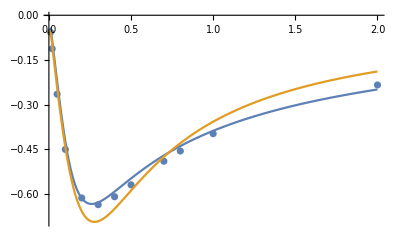

```mathematica
Clear[τ];
pressure={{100.,-0.004086899527429505},{50.,-0.008344050869667123},{20.,-0.021896677301376795},{10.,-0.046087643115920715},{5.,-0.09630124346005746},{2.,-0.2339294172437545},{1.,-0.3974527307359897},{0.5,-0.568975304838332},{0.2,-0.6130850161319591},{0.1,-0.45012115926748797},{0.05,-0.2647981458504634},{0.02,-0.1126510593168095},{0.01,-0.056928288413405734},{0.3,-0.6356377700725309},{0.4,-0.6090043327111337},{0.7,-0.4898532726109614},{0.8,-0.45550136224842336}};
P0=ListPlot[pressure];
Show[P0,Plot[{-(4 τ+15 τ^2)/(1+28 τ^2+20 τ^3),-(5τ)/(1+13 τ^2)},{τ,0.01,2},PlotRange->All],PlotRange->{{0.01,2},All}]
```

```mathematica
Clear[χ1,χ2,χ3,χ3]
{BCrhs,BC}=Normal[CoefficientArrays[
{-(un-vnW)+χ1 (pp-θW),
-1/χ2 σnt+(ut+2/1 mnnt-vtW),
-mnnn+χ3(σnn),
-mntt+χ4(σtt)},{pp,un,ut,σnn,σnt,σtt,mnnn,mnnt,mntt,mttt}]]
```

{{vnW-θW χ1,-vtW,0,0},{{χ1,-1,0,0,0,0,0,0,0,0},{0,0,1,0,-1/χ2,0,0,2,0,0},{0,0,0,χ3,0,0,-1,0,0,0},{0,0,0,0,0,χ4,0,0,-1,0}}}

```mathematica
R0=0.5;
R1=2.0;
τ=0.1;
χ=1.0;
χeps=1;
v0=1;
eps=0.00001;

A0=0.0;
A1=0.0;
A2=0.0;

scaling={C2->τ C2,C6->C6/τ,K1->(BI[1,λ2 R1/τ])^-1 K1,K2->(BK[0,λ2 R0/τ])^-1 K2,K3->(BK[0,λ2 R0/τ])^-1 K3,K4->(BI[0,λ2 R1/τ])^-1 K4,K5->(BK[3,λ3 R0/τ])^-1 K5,K6->(BI[3,λ3 R1/τ])^-1 K6,K7->(BK[1,λ3 R0/τ])^-1 K7,K8->(BI[1,λ3 R1/τ])^-1 K8};
scaling1={};
```

```mathematica
U[r_,θ_]:={p[r,θ],nn[r]ur[r,θ],uθ[r,θ],σrr[r,θ],nn[r]σrθ[r,θ],σθθ[r,θ],nn[r]mrrr[r,θ],mrrθ[r,θ],nn[r]mrθθ[r,θ],mθθθ[r,θ]};nn[R0]=-1;
nn[R1]=1;

solbc=Solve[(Join[
coef[Expand[BC.U[R0,θ]+BCrhs/.{θW->0,vnW->0,vtW->0,χ1->eps,χ2->1/eps,χ3->χ,χ4->χ}],{Cos[θ],Sin[θ]}],
coef[Expand[BC.U[R1,θ]+BCrhs/.{θW->-(5τ)/(1+13 τ^2)Cos[θ],vnW->v0 Cos[θ],vtW->-v0 Sin[θ],χ1->1/eps,χ2->1/eps,χ3->χeps,χ4->χeps}],{Cos[θ],Sin[θ]}]
]/.scaling)==0,{C1,C2,C3,C4,C5,C6,C7,C8,K1,K2,K3,K4,K5,K6,K7,K8}]⟦1⟧
```

{C1→-3.09916,C2→-0.14831,C3→0.,C4→0.,C5→-2.94121,C6→-1.23403,C7→0.,C8→0.,K1→0.00910081,K2→0.0150835,K3→0.,K4→0.,K5→-0.000686415,K6→0.00182389,K7→0.,K8→0.}

```mathematica
CForm[{C1,C2,C3,C4,C5,C6,C7,C8,K1,K2,K3,K4}/.scaling/.solbc]
```

List(-3.7493457286826626,-0.0001748532577469614,0.,0.,-8.121139559813377,-2207.9530113872297,0.,0.,-2.660553333968104e-83,4.9870629820977434e17,0.,0.)

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

pC[x_,y_]=p[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{ux[x_,y_],uy[x_,y_]}={ur[√(x^2+y^2),ArcTan[x,y]],uθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;

{{σxx[x_,y_],σxy[x_,y_]},{σyx[x_,y_],σyy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{σrr[√(x^2+y^2),ArcTan[x,y]],σrθ[√(x^2+y^2),ArcTan[x,y]]},{σrθ[√(x^2+y^2),ArcTan[x,y]],σθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[pC[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

```mathematica
Plot3D[ux[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

```mathematica
Plot3D[Norm[{ux[x,y],uy[x,y]}],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

0-1-2 system (Type A)

## first order 0-1-2-System with 2-relaxation

### Final Result

```mathematica
coef[expr_,var_]:=Flatten[Normal[CoefficientArrays[expr,var]]]
Coef[expr_,var_]:=Normal[CoefficientArrays[expr,var]]
$Assumptions={p0>0,RT0>0,u0>0,r>0,ξ>0, Cot[θ]>0,Kn>0,a>0,b>0};
```

```mathematica
Clear[χ,α,eps,ϵ,τ,a0,b0,c0,d0,α0,κ0,γ0,ω0,a,b,c,d,α,β,γ,κ,ω,C0,C1,C2,C3,C4,C5,C6,C7,C8,C9,C10,C11,C12,K1,K2,K3,K4,K5,K6,K7,K8,K9,K10,K11,K12]

ur[r_,θ_] = a0[r]+Cos[θ]a[r];
uθ[r_,θ_] = b0[r]+Sin[θ] b[r];

u[r_,θ_]={ur[r,θ],uθ[r,θ],0};

p[r_,θ_] = d0[r]+d[r]Cos[θ];


σrr[r_,θ_]=Cos[θ] γ[r]+γ0[r];
σθθ[r_,θ_]=Cos[θ] ω[r]+ω0[r];
σrθ[r_,θ_]=κ0[r]+Sin[θ]κ[r];
σzz[r_,θ_]=-σrr[r,θ]-σθθ[r,θ];

σ[r_,θ_]={{σrr[r,θ],σrθ[r,θ],0},{σrθ[r,θ],σθθ[r,θ],0},{0,0,σzz[r,θ]}};
```

```mathematica
withτ={r->r/τ};

a0[r_]=2 C1/r/.withτ;
b0[r_]=2(C2/(2 r)+r C4)/.withτ;
d0[r_]=C3/.withτ;
κ0[r_]=C2/r^2/.withτ;
γ0[r_]=(2 C1)/r^2/.withτ;
ω0[r_]=-(2 C1)/r^2/.withτ;

a[r_]=2(-C5/(2 r^2)+1/2 r^2 C6+C7+C8 Log[r])/.withτ;
b[r_]=2(-C7-C8-C5/(2 r^2)-(3 C6 r^2)/2-C8 Log[r])/.withτ;
d[r_]=-(2 C8)/r+4 C6 r/.withτ;
κ[r_]=-(2 C5)/r^3+2 C6 r/.withτ;
γ[r_]=-(2 C5)/r^3-(2 C8)/r-2 C6 r/.withτ;
ω[r_]=(2 C5)/r^3+(2 C8)/r+2 C6 r/.withτ;
```

```mathematica
FunctionExpand[coef[Div1[u[r,θ]],{Cos[θ],Sin[θ]}]]
FunctionExpand[coef[Grad0[p[r,θ]]+Div2[σ[r,θ]],{Cos[θ],Sin[θ]}]]
Expand[FunctionExpand[coef[1/2(Grad1[u[r,θ]]+Transpose[Grad1[u[r,θ]]])+1/τ σ[r,θ],{Cos[θ],Sin[θ]}]]]
```

{0}

{0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coef[Expand[ur[R0,θ]-p[R0,θ]],{Cos[θ],Sin[θ]}]
coef[Expand[σrθ[R0,θ]-uθ[R0,θ]],{Cos[θ],Sin[θ]}]
```

{-C3+(2 C1 τ)/R0,2 C7+(C6 R0^2)/τ^2-(4 C6 R0)/τ+(2 C8 τ)/R0-(C5 τ^2)/R0^2+2 C8 Log[R0/τ],0}

{-(2 C4 R0)/τ-(C2 τ)/R0+(C2 τ^2)/R0^2,0,2 C7+2 C8+(3 C6 R0^2)/τ^2+(2 C6 R0)/τ+(C5 τ^2)/R0^2-(2 C5 τ^3)/R0^3+2 C8 Log[R0/τ]}

### With Boundary Conditions

```mathematica
R0=0.2;
R1=1.0;
τ=0.15;
χ2=1.0;

v0=1.0;
eps=0.0001;

scaling={};
scaling1={};
```

```mathematica
solbc=Solve[(Join[
(* inner wall R = R0 *)
coef[Expand[1/eps ur[R0,θ]+p[R0,θ]],{Cos[θ],Sin[θ]}],
coef[Expand[σrθ[R0,θ] +χ2(uθ[R0,θ])],{Cos[θ],Sin[θ]}],

(* outer boundary/inflow R = R1 *)
coef[Expand[1/eps(ur[R1,θ]-v0 Cos[θ])-p[R1,θ]],{Cos[θ],Sin[θ]}],
coef[Expand[eps σrθ[R1,θ]-(uθ[R1,θ]-v0 Sin[θ])],{Cos[θ],Sin[θ]}]

]/.scaling)==0,{C1,C2,C3,C4,C5,C6,C7,C8}]⟦1⟧
```

{C1→0.,C2→0.,C3→0.,C4→0.,C5→-1.12148,C6→-0.0472391,C7→-0.596932,C8→1.12486}

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

pC[x_,y_]=p[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{ux[x_,y_],uy[x_,y_]}={ur[√(x^2+y^2),ArcTan[x,y]],uθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{σxx[x_,y_],σxy[x_,y_]},{σyx[x_,y_],σyy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{σrr[√(x^2+y^2),ArcTan[x,y]],σrθ[√(x^2+y^2),ArcTan[x,y]]},{σrθ[√(x^2+y^2),ArcTan[x,y]],σθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[pC[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

```mathematica
Plot3D[ux[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

```mathematica
Plot3D[σxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

### With Boundary Conditions (large)

```mathematica
Clear[χ1,χ2,χ3,χ3]
{BCrhs,BC}=Normal[CoefficientArrays[
{-(sn-vnW)+χ1((θ-θW)+Rnn),
-Rnt+χ2(st-vtW)},{θ,sn,st,Rnn,Rnt,Rtt}]]
```

{{vnW-θW χ1,-vtW χ2},{{χ1,-1,0,χ1,0,0},{0,0,χ2,0,-1,0}}}

```mathematica
{{vnW-θW χ1,-vtW χ2},{{χ1,-1,0,χ1,0,0},{0,0,χ2,0,-1,0}}}/.{θW->0,χ1->ϵ,χ2->1/ϵ}
```

{{vnW,-vtW/ϵ},{{ϵ,-1,0,ϵ,0,0},{0,0,1/ϵ,0,-1,0}}}

```mathematica
R0=1/2;
R1=2;
τ=1.0;

χ=1;
v0=1;
eps=10^-5;

A0=0;
A1=0;
A2=0;

scaling={C1->C1/eps,C2->C2/eps};
scaling1={};
```

```mathematica
U[r_,θ_]:={theta[r,θ],nn[r]sr[r,θ],sθ[r,θ],Rrr[r,θ],nn[r]Rrθ[r,θ],Rθθ[r,θ]};
nn[R0]=-1;
nn[R1]=1;

solbc=Solve[(DiagonalMatrix[{1,1,1,1,1,eps,1,1,1,1,1,eps}].Join[
coef[Expand[BC.U[R0,θ]+BCrhs/.{θW->0,vnW->0,vtW->0,χ1->eps,χ2->1/eps}],{Cos[θ],Sin[θ]}],
coef[Expand[BC.U[R1,θ]+BCrhs/.{θW->0,vnW->v0 Cos[θ],vtW->-v0 Sin[θ],χ1->eps,χ2->1/eps}],{Cos[θ],Sin[θ]}]
]/.scaling)==0,{C1,C2,C3,C4,C5,C6,C7,C8}]⟦1⟧
```

Dot::dotsh: Tensors {{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/100000, 0, 0, 0, 0, 0, 0}, {0, 0, 0, « 6 », 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/100000}} and {Rrr[1/2, θ]/100000 + sr[1/2, θ] + theta[1/2, θ]/100000, Rrθ[1/2, θ] + 100000\ sθ[1/2, θ], Rrr[2, θ]/100000 - sr[2, θ] + theta[2, θ]/100000, -Rrθ[2, θ] + 100000\ sθ[2, θ], 1, 0, 0, 100000} have incompatible shapes.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

θC[x_,y_]=theta[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{sx[x_,y_],sy[x_,y_]}={sr[√(x^2+y^2),ArcTan[x,y]],sθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{Rxx[x_,y_],Rxy[x_,y_]},{Ryx[x_,y_],Ryy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{Rrr[√(x^2+y^2),ArcTan[x,y]],Rrθ[√(x^2+y^2),ArcTan[x,y]]},{Rrθ[√(x^2+y^2),ArcTan[x,y]],Rθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {sx[x_, y_], sy[x_, y_]} and {x\ sr[√Power[« 2 »] + Power[« 2 »], ArcTan[x, y]]/√x^2 + y^2 - y\ sθ[√Power[« 2 »] + Power[« 2 »], ArcTan[x, y]]/√x^2 + y^2, y\ sr[√Power[« 2 »] + Power[« 2 »], ArcTan[x, y]]/√x^2 + y^2 + x\ sθ[√Power[« 2 »] + Power[« 2 »], ArcTan[x, y]]/√x^2 + y^2}/. {} ⟦ 1 ⟧ are not the same shape.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {{Rxx[x_, y_], Rxy[x_, y_]}, {Ryx[x_, y_], Ryy[x_, y_]}} and {{x\ (x\ Power[« 2 »]\ Rrr[« 2 »] - y\ Power[« 2 »]\ Rrθ[« 2 »])/√Power[« 2 »] + Power[« 2 »] - y\ (x\ Power[« 2 »]\ Rrθ[« 2 »] - y\ Power[« 2 »]\ Rθθ[« 2 »])/√Power[« 2 »] + Power[« 2 »], x\ (y\ Power[« 2 »]\ Rrr[« 2 »] + x\ Power[« 2 »]\ Rrθ[« 2 »])/√Power[« 2 »] + Power[« 2 »] - y\ (y\ Power[« 2 »]\ Rrθ[« 2 »] + x\ « 1 »\ Rθθ[« 2 »])/√Power[« 2 »] + Power[« 2 »]}, {y\ (« 1 » - « 1 »)/√Power[« 1 »] + « 1 » + « 1 »/√« 1 », « 1 » + « 1 »}} « 2 »  « 1 » are not the same shape.

```mathematica
Plot3D[θC[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1],PlotRange->All]
```

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[sx[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

```mathematica
Plot3D[Rxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

## first order 0-1-2-system with 1-2-relaxation

### Final Result

```mathematica
coef[expr_,var_]:=Flatten[Normal[CoefficientArrays[expr,var]]]
Clear[A0,A1,A2,τ,λ1,a0,b0,d0,κ0,γ0,ω0,a,b,d,γ,κ,ω,C1,C2,C3,C4,K1,K2,K3,K4]

sr[r_,θ_] = a0[r]+a[r]Cos[θ];
sθ[r_,θ_] = b0[r]+b[r]Sin[θ];

s[r_,θ_]={sr[r,θ],sθ[r,θ],0};

theta[r_,θ_] = d0[r]+d[r]Cos[θ];


Rrr[r_,θ_]= γ0[r]+γ[r]Cos[θ];
Rθθ[r_,θ_]=ω0[r]+ω[r]Cos[θ];
Rrθ[r_,θ_]=κ0[r]+κ[r]Sin[θ];
Rzz[r_,θ_]=-Rrr[r,θ]-Rθθ[r,θ];

R[r_,θ_]={{Rrr[r,θ],Rrθ[r,θ],0},{Rrθ[r,θ],Rθθ[r,θ],0},{0,0,Rzz[r,θ]}};

F[r_,θ_]=A0+A2 r^2+A1 Cos[θ];
```

```mathematica
λ1=√2;
BI[i_,x_]=BesselI[i,x];
BK[i_,x_]=BesselK[i,x];

withτ={r->r/τ};

a[r_]=τ(2 A1 r)/3-C2+C1/r^2-(√2 K2 BI[1,λ1 r])/r+(√2 K1 BK[1,λ1 r])/r/.withτ;
b[r_]=-τ(A1 r)/3+C2+C1/r^2+K2 (BI[0,λ1 r]+BI[2,λ1 r])+K1 (BK[0,λ1 r]+BK[2,λ1 r])/.withτ;

d[r_]=-1/3 τ A1 (-2+r^2)+C1/r+C2 r/.withτ;
γ[r_]=-τ A1/3+(2 C1)/r^3+(2 K2 BI[2,λ1 r])/r+(2 K1 BK[2,λ1 r])/r/.withτ;

ω[r_]=-(2 C1)/r^3-(2 K2 BI[2,λ1 r])/r-(2 K1 BK[2,λ1 r])/r/.withτ;
κ[r_]=τ A1/3+(2 C1)/r^3+K2((2 BI[0,λ1 r])/r-√2 BI[1,λ1 r]-(2 √2 BI[1,λ1 r])/r^2)+K1((2 BK[0,λ1 r])/r+√2 BK[1,λ1 r]+(2 √2 BK[1,λ1 r])/r^2)/.withτ;


d0[r_]=-τ(A0 r^2)/4+τ^3(2 A2 r^2)/3-τ^3(A2 r^4)/16+C3+C4 Log[r]/.withτ;

a0[r_]=τ(A0 r)/2+τ^3(A2 r^3)/4-C4/r/.withτ;
b0[r_]=K3 BK[1,λ1 r]+K4 BI[1,λ1 r]/.withτ;

γ0[r_]=-τ A0/6-τ^3(5 A2 r^2)/12-C4/r^2/.withτ;
κ0[r_]=-(K4 BI[2,λ1 r])/(√2)+(K3 BK[2,λ1 r])/(√2)/.withτ;
ω0[r_]=-τ A0/6+τ^3(A2 r^2)/12+C4/r^2/.withτ;
```

```mathematica
TraceFreeSym2[mat_]:=1/2(mat+Transpose[mat])-1/3 Tr[mat]IdentityMatrix[3];
```

```mathematica
FunctionExpand[
{coef[Div1[s[r,θ]]-F[r,θ],{Cos[θ],Sin[θ]}],
coef[Grad0[theta[r,θ]]+Div2[R[r,θ]]+1/τ s[r,θ],{Cos[θ],Sin[θ]}],
coef[TraceFreeSym2[Grad1[s[r,θ]]]+1/τ R[r,θ],{Cos[θ],Sin[θ]}]
}]
```

{{0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
FunctionExpand[coef[Grad0[theta[r,θ]]-1/2 τ Laplace1[s[r,θ]]-1/6 τ Grad0[Div1[s[r,θ]]]+1/τ s[r,θ],{Cos[θ],Sin[θ]}]]
```

{0,0,0,0,0,0,0,0,0}

### With Boundary Conditions

#### tau = 0.01, A0 = 0, A1 = 0.2, A1 = 0.1, θ0 = 2, θ1 = 1

```mathematica
R0=0.5;
R1=2.0;
τ=0.01;
χ=1;
θ0=2;
θ1=1;
uW0=τ;
A0=0;
A1=0.2;
A2=0.1;

scaling={};
scaling1={};
```

```mathematica
scaling={};
nn[R0]=-1;
nn[R1]=1;
solbc=Solve[(Join[
(* inner wall R = R0 *)
coef[Expand[nn[R0]sr[R0,θ]-χ((theta[R0,θ]-θ0)+Rrr[R0,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[nn[R0]Rrθ[R0,θ] -χ(sθ[R0,θ]-uW0 Sin[θ])],{Cos[θ],Sin[θ]}],

(* outer boundary R = R1 *)
coef[Expand[nn[R1]sr[R1,θ]-χ((theta[R1,θ]-θ1)+Rrr[R1,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[nn[R1]Rrθ[R1,θ] -χ(sθ[R1,θ])],{Cos[θ],Sin[θ]}]

]/.scaling)==0,{K1,K2,K3,K4,C1,C2,C3,C4}]⟦1⟧
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-3.89162, -1., 0., 0., 0., 0., 0., 0., 2.03588}, {0., 0., -49., -0.020416, 0., 0., -2.6263×10^27, -2.02325×10^-33, 1.59933}, « 5 », {0., 0., -1., -0.00002475, 0., 0., -5.53558×10^121, -6.29101×10^-125, 0.134}} may contain significant numerical errors.

Solve::svars: Equations may not give solutions for all "solve" variables.

{K2→1.08215×10^-127-4.73477×10^-162 K1,K4→0.-1.13252×10^-246 K3,C1→-258.621-1.05361×10^-31 K1,C2→0.140395+2.60794×10^-36 K1,C3→-23.2246,C4→6.49099}

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

θC[x_,y_]=theta[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc/.{K1->0,K3->0};

{sx[x_,y_],sy[x_,y_]}={sr[√(x^2+y^2),ArcTan[x,y]],sθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{Rxx[x_,y_],Rxy[x_,y_]},{Ryx[x_,y_],Ryy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{Rrr[√(x^2+y^2),ArcTan[x,y]],Rrθ[√(x^2+y^2),ArcTan[x,y]]},{Rrθ[√(x^2+y^2),ArcTan[x,y]],Rθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[θC[x,y],{x,-2,2},{y,-2,2},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1],PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[sx[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

```mathematica
Plot3D[Rxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

#### tau = 0.1, A0 = 0, A1 = 0.2, A1 = 0.1, θ0 = 2, θ1 = 1

```mathematica
R0=0.5;
R1=2.0;
τ=0.1;
χ=1;
θ0=2;
θ1=1;
uW0=τ;
A0=0;
A1=0.2;
A2=0.1;

scaling={};
scaling1={};
```

```mathematica
scaling={};
nn[R0]=-1;
nn[R1]=1;
solbc=Solve[(Join[
(* inner wall R = R0 *)
coef[Expand[nn[R0]sr[R0,θ]-χ((theta[R0,θ]-θ0)+Rrr[R0,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[nn[R0]Rrθ[R0,θ] -χ(sθ[R0,θ]-uW0 Sin[θ])],{Cos[θ],Sin[θ]}],

(* outer boundary R = R1 *)
coef[Expand[nn[R1]sr[R1,θ]-χ((theta[R1,θ]-θ1)+Rrr[R1,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[nn[R1]Rrθ[R1,θ] -χ(sθ[R1,θ])],{Cos[θ],Sin[θ]}]

]/.scaling)==0,{K1,K2,K3,K4,C1,C2,C3,C4}]⟦1⟧
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-1.36944, -1., 0., 0., 0., 0., 0., 0., 2.00016}, {0., 0., -4., -0.256, 0., 0., -5.97747, -0.000324076, 0.0933333}, « 5 », {0., 0., -1., -0.00225, 0., 0., -4.67223×10^11, -6.41921×10^-14, 0.14}} may contain significant numerical errors.

{K1→53.9717,K2→1.26255×10^-15,K3→0.,K4→0.,C1→-1.9506,C2→0.143799,C3→1.84483,C4→0.113421}

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

θC[x_,y_]=theta[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{sx[x_,y_],sy[x_,y_]}={sr[√(x^2+y^2),ArcTan[x,y]],sθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{Rxx[x_,y_],Rxy[x_,y_]},{Ryx[x_,y_],Ryy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{Rrr[√(x^2+y^2),ArcTan[x,y]],Rrθ[√(x^2+y^2),ArcTan[x,y]]},{Rrθ[√(x^2+y^2),ArcTan[x,y]],Rθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[θC[x,y],{x,-2,2},{y,-2,2},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1],PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[sx[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

```mathematica
Plot3D[Rxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

```mathematica
d
```

#### tau = 1.0, A0 = 0, A1 = 0.2, A1 = 0.1, θ0 = 2, θ1 = 1

```mathematica
R0=0.5;
R1=2.0;
τ=1.0;
χ=1;
θ0=2;
θ1=1;
uW0=τ;
A0=0;
A1=0.2;
A2=0.1;

scaling={};
scaling1={};
```

```mathematica
scaling={};
nn[R0]=-1;
nn[R1]=1;
solbc=Solve[(Join[
(* inner wall R = R0 *)
coef[Expand[nn[R0]sr[R0,θ]-χ((theta[R0,θ]-θ0)+Rrr[R0,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[nn[R0]Rrθ[R0,θ] -χ(sθ[R0,θ]-uW0 Sin[θ])],{Cos[θ],Sin[θ]}],

(* outer boundary R = R1 *)
coef[Expand[nn[R1]sr[R1,θ]-χ((theta[R1,θ]-θ1)+Rrr[R1,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[nn[R1]Rrθ[R1,θ] -χ(sθ[R1,θ])],{Cos[θ],Sin[θ]}]

]/.scaling)==0,{K1,K2,K3,K4,C1,C2,C3,C4}]⟦1⟧
```

{K1→0.188036,K2→0.00360406,K3→0.,K4→0.,C1→-0.148693,C2→0.172572,C3→1.2977,C4→-0.103586}

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

θC[x_,y_]=theta[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{sx[x_,y_],sy[x_,y_]}={sr[√(x^2+y^2),ArcTan[x,y]],sθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{Rxx[x_,y_],Rxy[x_,y_]},{Ryx[x_,y_],Ryy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{Rrr[√(x^2+y^2),ArcTan[x,y]],Rrθ[√(x^2+y^2),ArcTan[x,y]]},{Rrθ[√(x^2+y^2),ArcTan[x,y]],Rθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[θC[x,y],{x,-2,2},{y,-2,2},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1],PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[sx[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

```mathematica
Plot3D[Rxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

#### tau = 10.0, A0 = 0, A1 = 0.2, A1 = 0.1, θ0 = 2, θ1 = 1

```mathematica
R0=0.5;
R1=2.0;
τ=10.0;
χ=1;
θ0=2;
θ1=1;
uW0=τ;
A0=0;
A1=0.2;
A2=0.1;

scaling={};
scaling1={};
```

```mathematica
scaling={};
nn[R0]=-1;
nn[R1]=1;
solbc=Solve[(Join[
(* inner wall R = R0 *)
coef[Expand[nn[R0]sr[R0,θ]-χ((theta[R0,θ]-θ0)+Rrr[R0,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[nn[R0]Rrθ[R0,θ] -χ(sθ[R0,θ]-uW0 Sin[θ])],{Cos[θ],Sin[θ]}],

(* outer boundary R = R1 *)
coef[Expand[nn[R1]sr[R1,θ]-χ((theta[R1,θ]-θ1)+Rrr[R1,θ])],{Cos[θ],Sin[θ]}],
coef[Expand[nn[R1]Rrθ[R1,θ] -χ(sθ[R1,θ])],{Cos[θ],Sin[θ]}]

]/.scaling)==0,{K1,K2,K3,K4,C1,C2,C3,C4}]⟦1⟧
```

{K1→0.189002,K2→-0.648699,K3→0.,K4→0.,C1→-0.188505,C2→1.43519,C3→0.117163,C4→-0.00429615}

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

θC[x_,y_]=theta[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{sx[x_,y_],sy[x_,y_]}={sr[√(x^2+y^2),ArcTan[x,y]],sθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{Rxx[x_,y_],Rxy[x_,y_]},{Ryx[x_,y_],Ryy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{Rrr[√(x^2+y^2),ArcTan[x,y]],Rrθ[√(x^2+y^2),ArcTan[x,y]]},{Rrθ[√(x^2+y^2),ArcTan[x,y]],Rθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[θC[x,y],{x,-2,2},{y,-2,2},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1],PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[sx[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

```mathematica
Plot3D[Rxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

-Graphics3D-

### With Boundary Conditions (large radius)

```mathematica
Clear[χ,χ1,χ2,χ3,χ3]
{BCrhs,BC}=Normal[CoefficientArrays[
{-(sn-vnW)+χ((θ-θW)+Rnn),
-Rnt+χ st},{θ,sn,st,Rnn,Rnt,Rtt}]]
```

{{vnW-θW χ,0},{{χ,-1,0,χ,0,0},{0,0,χ,0,-1,0}}}

```mathematica
R0=0.5;
R1=2.0;
τ=0.1;
ζ=1.0;
χ=1;
θ0=2.0;
θ1=1.0;
uW0=0.0;
A0=0.0;
A1=0.1;
A2=-0.1;

scaling={C1->C1,C2->C2,K1->BK[1,λ1 R0/τ]^-1 K1/(τ),K2->BI[1,λ1 R1/τ]^-1 K2/(τ),
K3->BK[1,λ1 R0/τ]^-1 K3,K4->BI[1,λ1 R1/τ]^-1 K4};
scaling1={};
```

```mathematica
U[r_,θ_]:={theta[r,θ],nn[r]sr[r,θ],sθ[r,θ],Rrr[r,θ],nn[r]Rrθ[r,θ],Rθθ[r,θ]};
nn[R0]=-1;
nn[R1]=1;

solbc=Solve[(Join[
coef[Expand[BC.U[R0,θ]+BCrhs/.{θW->θ0,vnW->0,vtW->0,χ1->eps,χ2->1/eps}],{Cos[θ],Sin[θ]}],
coef[Expand[BC.U[R1,θ]+BCrhs/.{θW->θ1,vnW->0,vtW->0,χ1->eps,χ2->1/eps}],{Cos[θ],Sin[θ]}]
]/.scaling)==0,{C1,C2,C3,C4,K1,K2,K3,K4}]⟦1⟧
```

{C1→-0.935184,C2→0.0718083,C3→3.79149,C4→-1.30831,K1→-0.000150497,K2→9.00749×10^-6,K3→0.,K4→0.}

```mathematica
CForm[{C1,C2,C3,C4,K1,K2,K3,K4}/.scaling/.solbc]
```

List(-0.9351837633174386,0.07180825974284018,3.79149457833139,-1.3083111049166367,-3.577337931978802,
   6.33324623915661e-16,0.,0.)

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

θC[x_,y_]=theta[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{sx[x_,y_],sy[x_,y_]}={sr[√(x^2+y^2),ArcTan[x,y]],sθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{Rxx[x_,y_],Rxy[x_,y_]},{Ryx[x_,y_],Ryy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{Rrr[√(x^2+y^2),ArcTan[x,y]],Rrθ[√(x^2+y^2),ArcTan[x,y]]},{Rrθ[√(x^2+y^2),ArcTan[x,y]],Rθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[θC[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1],PlotRange->All]
```

```mathematica
Plot3D[sx[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

```mathematica
Plot3D[Rxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

### With Boundary Conditions (large, angular)

```mathematica
Clear[χ1,χ2,χ3,χ3]
{BCrhs,BC}=Normal[CoefficientArrays[
{-(sn-vnW)+χ1((θ-θW)+Rnn),
-Rnt+χ2(st-vtW)},{θ,sn,st,Rnn,Rnt,Rtt}]]
```

{{vnW-θW χ1,-vtW χ2},{{χ1,-1,0,χ1,0,0},{0,0,χ2,0,-1,0}}}

```mathematica
{BCrhs,BC}/.{vnW->0,θW->0,χ1->χ,χ2->χ}
```

{{0,-vtW χ},{{χ,-1,0,χ,0,0},{0,0,χ,0,-1,0}}}

```mathematica
R0=1/2;
R1=2;
τ=.;

χ=1;
v0=1;

A0=0;
A1=0;
A2=0;

scaling={C1->C1,C2->C2,K1->BK[1,λ1 R0/τ]^-1 K1/(τ),K2->BI[1,λ1 R1/τ]^-1 K2/(τ),
K3->BK[1,λ1 R0/τ]^-1 K3,K4->BI[1,λ1 R1/τ]^-1 K4};
scaling1={};
```

```mathematica
U[r_,θ_]:={theta[r,θ],nn[r]sr[r,θ],sθ[r,θ],Rrr[r,θ],nn[r]Rrθ[r,θ],Rθθ[r,θ]};
nn[R0]=-1;
nn[R1]=1;

solbc=Solve[(Join[
coef[Expand[BC.U[R0,θ]+BCrhs/.{θW->0,vnW->0,vtW->-v0 Sin[θ],χ1->χ,χ2->χ}],{Cos[θ],Sin[θ]}],
coef[Expand[BC.U[R1,θ]+BCrhs/.{θW->0,vnW->0,vtW->0,χ1->χ,χ2->χ}],{Cos[θ],Sin[θ]}]
]/.scaling)==0,{C1,C2,C3,C4,K1,K2,K3,K4}]⟦1⟧
```

{C1→0.802317,C2→-0.00182436,C3→0.,C4→0.,K1→-0.0257155,K2→5.829×10^-7,K3→0.,K4→0.}

```mathematica
C3=C4=K3=K4=0;
{bBC,ABC}=FunctionExpand[Simplify[Normal[CoefficientArrays[Select[Join[
coef[Expand[BC.U[R0,θ]+BCrhs/.{θW->0,vnW->0,vtW->-v0 Sin[θ],χ1->χ,χ2->χ}],{Cos[θ],Sin[θ]}],
coef[Expand[BC.U[R1,θ]+BCrhs/.{θW->0,vnW->0,vtW->0,χ1->χ,χ2->χ}],{Cos[θ],Sin[θ]}]
],Length[#]>0&],{C1,C2,K1,K2}]]]]

scale1=DiagonalMatrix[{τ^0,τ^-1,1,1}];
scale2=DiagonalMatrix[{τ^-3,τ^0,(τ^2 BesselK[0,λ1/(R1 τ)])^-1,(BesselI[0,λ1/(R0 τ)])^-1}];
MatrixForm[Expand[scale1.ABC.scale2/.{τ->0.01}]]
```

```mathematica
basis[φ_]={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};

θC[x_,y_]=theta[√(x^2+y^2),ArcTan[x,y]]/.scaling/.solbc;

{sx[x_,y_],sy[x_,y_]}={sr[√(x^2+y^2),ArcTan[x,y]],sθ[√(x^2+y^2),ArcTan[x,y]]}.basis[ArcTan[x,y]]/.scaling/.solbc;
{{Rxx[x_,y_],Rxy[x_,y_]},{Ryx[x_,y_],Ryy[x_,y_]}}=Transpose[basis[ArcTan[x,y]]].({{Rrr[√(x^2+y^2),ArcTan[x,y]],Rrθ[√(x^2+y^2),ArcTan[x,y]]},{Rrθ[√(x^2+y^2),ArcTan[x,y]],Rθθ[√(x^2+y^2),ArcTan[x,y]]}}.basis[ArcTan[x,y]])/.scaling/.solbc;
```

```mathematica
Plot3D[θC[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1],PlotRange->All]
```

```mathematica
Plot3D[sx[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotPoints->30,PlotRange->All,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```

```mathematica
Plot3D[Rxy[x,y],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->30,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],RegionFunction->Function[{x,y,z},R0<√(x^2+y^2)<R1]]
```